## 何为模型

Say you want to know (as Galileo did back in the late 1500s) how long it’s going to take a cannon ball dropped from each floor of the Tower of Pisa to hit the ground. Well, you could just measure it in each case and make a table of the results. Or you could do what is the essence of theoretical science: make a model that gives some kind of procedure for computing the answer rather than just measuring and remembering each case.

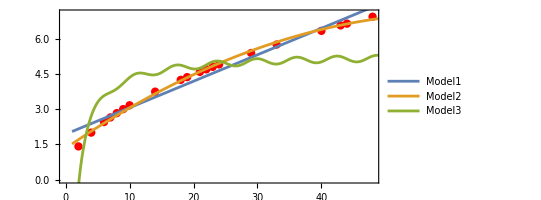

```mathematica
data=(SeedRandom[34535];{#,Sqrt[#]}&/@Sort[RandomSample[Range[50],20]]);
Show[
ListPlot[data,Frame->True,PlotRange->{0,Sqrt[50]},
PlotStyle->{Red,PointSize[.015]},AspectRatio->1/2],
Plot[Evaluate[{Fit[data,{1,x},x],Fit[data,{1,x,x^2},x],Fit[data,{1,1/x,Sin[x]},x]}],{x,1,50},PlotLegends->{"Model1","Model2","Model3"}]
]
```

## 类人任务

## 预训练网络

```mathematica
{{"[◼]", "NetBlockPlot3D"}}[NetModel["LeNet Trained on MNIST Data"]]
```

-Graphics3D-

```mathematica
Information[NetModel["LeNet Trained on MNIST Data"],"SummaryGraphic"]
```

-Graphics-

```mathematica
NetModel["LeNet Trained on MNIST Data"][{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{7,0,9,7,8,2,4,1,1,1}

```mathematica
Blur[-Graphics-,#]&/@Range[10]
NetModel["LeNet Trained on MNIST Data"][%](*随着模糊，逐渐认不出来*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{2,2,1,1,1,1,1,1,1,1}

```mathematica
#->ArrayPlot[{Drop[NetModel["LeNet Trained on MNIST Data"],-1][#]}/30,ImageSize->120,Frame->None,Mesh->True,ColorFunction->{{"[◼]", "ChatTechColors"}}["OrangeShort"] ]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}(*最后一层的数值*)
```

{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

## 特征空间

```mathematica
FeatureSpacePlot[Catenate[Cases[ResourceData["MNIST"],(x_->#):>(x->SetAlphaChannel[x,ColorNegate[x]]),{1},5(*数字个数*)]&/@Range[6](*数字范围*)],RandomSeeding->5,Frame->True,FrameTicks->None]
```

-Graphics-

```mathematica
Framed[FeatureSpacePlot[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},LabelingSize->60],FrameStyle->{GrayLevel[0,.3]}]
```

-Graphics-

```mathematica
FeatureSpacePlot3D[SeedRandom[123];#->SetAlphaChannel[#,ColorNegate[#]]&@@@RandomSample[ResourceData["MNIST"],50],FeatureExtractor->NetDrop[NetModel["LeNet Trained on MNIST Data"],-3]]
```

-Graphics3D-

## 网络内部

```mathematica
GraphicsGrid[Partition[Take[Image/@Take[NetModel["Wolfram ImageIdentify Net V1"],#][-Graphics-],50],10]]&/@{1,10}(*层数*)//GraphicsRow[#,ImageSize->Full]&
```

-Graphics-

## 计算不可约

The kinds of things that we normally do with our brains are presumably specifically chosen to avoid computational irreducibility. It takes special effort to do math in one’s brain. And it’s in practice largely impossible to “think through” the steps in the operation of any nontrivial program just in one’s brain.

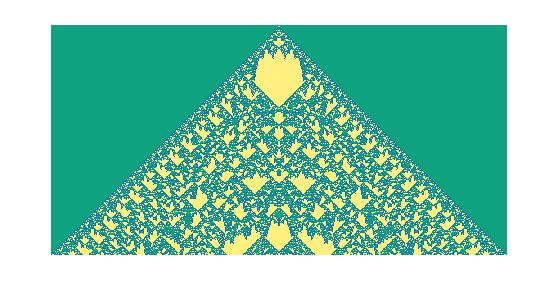

```mathematica
ArrayPlot[CellularAutomaton[{231968390,{5,1}},{{1},0},280],PixelConstrained->1,ColorRules->{0->RGBColor[Rational[1, 17], Rational[54, 85], Rational[127, 255], 0.2],1->RGBColor[Rational[1, 17], Rational[54, 85], 0.72],2->RGBColor[{Rational[1, 17], Rational[54, 85], Rational[127, 255]}],3->RGBColor[1, 0.9400000000000001, 0.5],4->RGBColor[Rational[1, 17], 0.46, 0.72]},FrameStyle->GrayLevel[0.71]]
```